Force Balance on a Scissor Truss

```mathematica
Manipulate[
Module[{w,h,θ1,θ2,sol,RA,RB,FAB,FAC,FAE,FBD,FBF,FCD,FCE,FDF,FEF,colC,colT,colC0,colT0,zero,scale},
w=5;h=5;
θ1=ArcTan[h/w];θ2=ArcTan[h/(2*w)];

sol=Quiet@Solve[N@{
(*(*reactions*)w*(-FA)+2*w*(-FB)+3*w*rb==0,ra+rb-FA-FB==0,*)
(*reactions*)w*FA+2*w*FB-3*w*rb==0,ra+rb-FA-FB==0,
(*A*)fae-fab*1/(√2)-fac*2/(√5)==0,
(*B*)fab*1/(√2)+fbd*1/(√5)-fbf*1/(√2)==0,fab*1/(√2)+fbf*1/(√2)-fbd*2/(√5)==0,
(*C*)fac*1/(√5)+fcd*1/(√2)-fce*1/(√2)==0,fac*2/(√5)-fce*1/(√2)-fcd*1/(√2)==0,
(*E*)fce*1/(√2)-FA==0,fef-fae+fce*1/(√2)==0,
(*F*)fbf*1/(√2)-FB==0,fdf-fef-fbf*1/(√2)==0
},{ra,rb,fab,fac,fae,fbd,fbf,fcd,fce,fdf,fef}][[1]];

RA=ra/.sol;RB=rb/.sol;FAB=-fab/.sol;
FAC=-fac/.sol;FAE=fae/.sol;FBD=-fbd/.sol;
FBF=fbf/.sol;FCD=-fcd/.sol;FCE=fce/.sol;
FDF=fdf/.sol;FEF=fef/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];
colC0[F_]:=If[F==0,Black,colC];colT0[F_]:=If[F==0,Black,colT];
zero[F_]:=If[F==0,Line,Arrow];
scale[F_]:=Rescale[F,{0,15}];

Graphics[{Thick,
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{2*w,0},{w,h}}],Polygon[{{3*w,0},{w,0},{2*w,h}}]},
Line[{{w,h},{3*w,0}}],Line[{{2*w,h},{0,0}}],

{Blue,
Arrow[{{w,0},{w,-h/2*scale[FA]}}],Arrow[{{2*w,0},{2*w,-h/2*scale[FB]}}],
If[#2≠0,Text[Style[Row@{Subscript[Style["F",Italic],#1]," = ",NumberForm[#2,{3,1}]," kN"},18],{#3,-h/2*scale[#2]},{0,1.2}]]&@@@{{"1",FA,w},{"2",FB,2*w}},
Arrow[{{0,-h/2*scale[RA]},{0,0}}],Arrow[{{3*w,-h/2*scale[RB]},{3*w,0}}],
If[#2≠0,Text[Style[Row@{Subscript[Style["R",Italic],#1]," = ",NumberForm[N@#2,{3,1}]," kN"},18],{#3,-h/2*scale[#2]},{0,1.2}]]&@@@{{"A",RA,0},{"D",RB,3*w}}},

Flatten@{If[#1<0,{colC0[#1],Arrowheads@{-0.045,0.045}},{colT0[#1],Arrowheads@{{0.045,0.4},{-0.045,0.6}}}],
zero[#1][#2],Text[Rotate[Style[Row@{" ",NumberForm[Abs@#1,{4,1}]," "},18,Background->White],#4],#3]}&@@@{
{FAB,{{0,0},{w,h}},{w/2,h/2},θ1},{FAC,{{0,0},{2*w,h}},{w,h/2},θ2},{FAE,{{0,0},{w,0}},{w/2,0},0},{FBD,{{w,h},{3*w,0}},{(w+3*w)/2,h/2},-θ2},{FCD,{{2*w,h},{3*w,0}},{2*w+w/2,h/2},-θ1},{FDF,{{3*w,0},{2*w,0}},{2*w+w/2,0},0},{FEF,{{w,0},{2*w,0}},{w+w/2,0},0}},

Flatten@{If[#1<0,{colC0[#1],Arrowheads@{-0.045,0.045}},{colT0[#1],Arrowheads@{{0.045,0.5},{-0.045,0.8}}}],
zero[#1][#2],Text[Rotate[Style[Row@{" ",NumberForm[Abs@#1,{4,1}]," "},18,Background->White],#4],#3]}&@@@{
{FBF,{{w,h},{2*w,0}},{w+0.65*w,0.35*h},-θ1},{FCE,{{2*w,h},{w,0}},{w+0.35*w,0.35*h},θ1}},

If[joints,Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15],#2,#3]&@@@{
{"A",{0,0},{1,0}},{"B",{w,h},{0,-1}},{"C",{2*w,h},{0,-1}},{"D",{3*w,0},{-1,0}},{"E",{w,0},{1.2,1.2}},{"F",{2*w,0},{-1.2,1.2}}}],

Text[Style[Row@{"all ",Style["tension",colT]," and ",Style["compression",colC]," forces are in kN"},17],{1.5*w,1.5*h}]
},PlotRange->{{-1.65,16.65},{-3.3,All}},ImageSize->{600,425}]
],
Grid@{{
"point loads (kN):",Spacer@10,
Control[{{FA,10,Subscript[Style["F",Italic],1]},0,15,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,10,Subscript[Style["F",Italic],2]},0,15,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{joints,False,"show joint labels"},{True,False}}]
}}
]
```

In this Demonstration the method of joints is used to solve the member forces in a scissor truss. The point loads (F_1, F_2) and reaction forces (R_A, R_D) are shown in blue. Set the point loads with sliders. Check "show joint labels" to show the labeled joints on the truss. Arrows that point outward represent compression forces (green) and arrows that point inward represent tension forces (red). Compression acts to shorten the member and tension acts to lengthen the member. The black members are zero forces; i.e., these members are neither in tension nor in compression so the force is 0 kN. The purpose of zero members is to provide stability and extra support to the structure in case another member fails. The member forces are shown on the diagram.





The method of sections is used to determine the member forces in the scissor truss. First, write out the lengths of the members (Figure 1):

for the equilateral triangles:

z_1=√(L^2+L^2)=√2 L,

for the scalene triangles:

z_2=√((2 L)^2+L^2)=√5 L,

where z is the length of the hypotenuse.

The reaction forces are solved for next. The sum of the moment about joint A and the sum of the forces in the y-direction are taken:

∑M_A=0=L F_1+2 L F_2-3 L R_D,

∑F_y=0=R_A-F_1-F_2+R_D,

where F_A and F_B are the vertical point load forces at joints A and B, and R_A and R_D are the reaction forces at joints A and D (all in kN).

Next, force balances in the x- and y-directions are done at the joints:

joint A:

∑F_x=0=-F_AB 1/(√2)-F_AC 2/(√5)+F_AE,

joint B:

∑F_y=0=F_AB 1/(√2)+F_BD 1/(√5)-F_BF 1/(√2),

∑F_x=0=F_AB 1/(√2)-F_BD 2/(√5)+F_BF 1/(√2),

joint C:

∑F_y=0=F_AC 1/(√5)+F_CD 1/(√2)-F_CE 1/(√2),

∑F_x=0=F_AC 2/(√5)-F_CD 1/(√2)-F_CE 1/(√2),

joint E:

∑F_y=0=F_CE 1/(√2)-F_1,

∑F_x=0=-F_AE+F_CE 1/(√2)+F_EF,

joint F:

∑F_y=0=F_BF 1/(√2)-F_2,

∑F_x=0=-F_BF 1/(√2)+F_DF-F_EF.

Figure 1

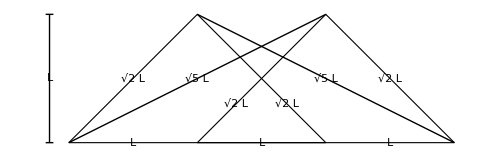

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

mechanical engineering

civil engineering

statics

truss

method of joints

force balance

scissor truss

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)